```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/josephcrandall/Documents/school/GW_Grad/2018_1Spring/ECE_6999_Thesis_Research/w12_04-02/roc_analytical

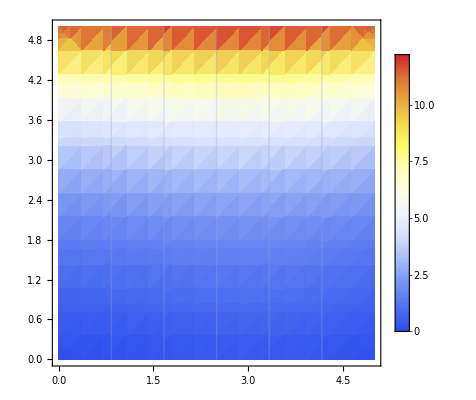

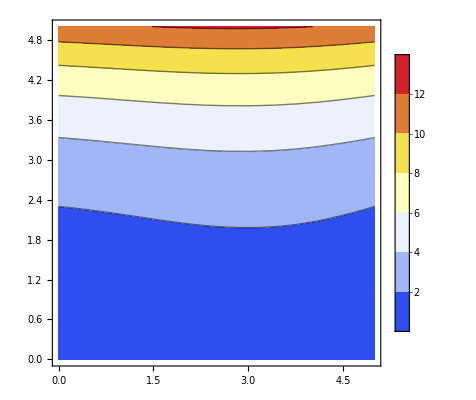

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
a=5;
b=5;
f0[x_,y_]:=x+ y;
f[x_,y_]:=f0[ x,y]/(Sinh [(π b)/a]) Sin[(π x)/a]  +Sinh[π y/a]
DensityPlot[f[x,y],{x,0,5},{y,0,5},Mesh->5, ColorFunction->"TemperatureMap",PlotLegends->Automatic]
ContourPlot[f[x,y],{x,0,5},{y,0,5}, ColorFunction->"TemperatureMap",PlotLegends->Automatic]
Plot3D[f[x,y],{x,0,5},{y,0,5},Mesh->4]  (*5^1 *) 
Plot3D[f[x,y],{x,0,5},{y,0,5},Mesh->25] (*5^2 *) 
Plot3D[f[x,y],{x,0,5},{y,0,5},Mesh->125] (*5^3 *) 
Plot3D[f[x,y],{x,0,5},{y,0,5},Mesh->625] (*5^4 *) 
(*Plot3D[f[x,y],{x,0,5},{y,0,5},Mesh->3125]*)
(*Plot3D[f[x,y],{x,0,5},{y,0,5},Mesh->15625]*)
```

```mathematica
This following points5 are taken at the top left corner of each grid box;
```

```mathematica
points5 = Table[{f[x,y]}, {x,Range[0,5,1]},{y,Range[0,5,1]}]//N; (*5^1 -> Step (5^-0) *) 
Export["points5.csv", points5];
points25 = Table[{f[x,y]}, {x,Range[0,5,0.2]},{y,Range[0,5,0.2]}]//N;  (*5^2 -> Step (5^-1)*)
Export["points25.csv", points25];
points125 = Table[{f[x,y]}, {x,Range[0,5,0.04]},{y,Range[0,5,0.04]}]//N;(*5^2 -> Step (5^-2)*)
Export["points125.csv", points125];
points625 = Table[{f[x,y]}, {x,Range[0,5,0.008]},{y,Range[0,5,0.008]}]//N; (*5^4* -> Step (5^-3)*)
Export["points625.csv", points625];
```

```mathematica
Grid[points5]//N
```

{f[0.,0.]} | {f[0.,1.]} | {f[0.,2.]} | {f[0.,3.]} | {f[0.,4.]} | {f[0.,5.]}
{f[1.,0.]} | {f[1.,1.]} | {f[1.,2.]} | {f[1.,3.]} | {f[1.,4.]} | {f[1.,5.]}
{f[2.,0.]} | {f[2.,1.]} | {f[2.,2.]} | {f[2.,3.]} | {f[2.,4.]} | {f[2.,5.]}
{f[3.,0.]} | {f[3.,1.]} | {f[3.,2.]} | {f[3.,3.]} | {f[3.,4.]} | {f[3.,5.]}
{f[4.,0.]} | {f[4.,1.]} | {f[4.,2.]} | {f[4.,3.]} | {f[4.,4.]} | {f[4.,5.]}
{f[5.,0.]} | {f[5.,1.]} | {f[5.,2.]} | {f[5.,3.]} | {f[5.,4.]} | {f[5.,5.]}

```mathematica
test5 =Table[10 i+j,{i,5},{j,5}]
```

{{11,12,13,14,15},{21,22,23,24,25},{31,32,33,34,35},{41,42,43,44,45},{51,52,53,54,55}}

```mathematica
Grid [test5]
```

11 | 12 | 13 | 14 | 15
21 | 22 | 23 | 24 | 25
31 | 32 | 33 | 34 | 35
41 | 42 | 43 | 44 | 45
51 | 52 | 53 | 54 | 55